# Electric Field by a plate

```mathematica
(* boundary value problem is *)
Φ[x,t,z]=-1/(4π)∫Φ[x',y',z'] dG/dn' da'
```

```mathematica
G[x_,y_,z_,xx_,yy_,zz_]:=1/(√((x-xx)^2+(y-yy)^2+(z-zz)^2))
```

```mathematica
D[G[x,y,z,xx,yy,zz],zz]
```

(z-zz)/(((x-xx)^2+(y-yy)^2+(z-zz)^2)^(3/2))

```mathematica
Integrate[1/(((x-xx)^2+bb^2)^(3/2)),{xx,-W,W},Assumptions->{(x-xx)^2+bb^2>0, bb≠0,W>0}]
```

(x (-1/(√(bb^2+(W-x)^2))+1/(√(bb^2+(W+x)^2)))+W (1/(√(bb^2+(W-x)^2))+1/(√(bb^2+(W+x)^2))))/bb^2

```mathematica
1/bb^2((W-x)/(√(bb^2+(W-x)^2))+(W+x)/(√(bb^2+(W+x)^2)))
```

```mathematica
Integrate[1/(((y-yy)^2+z^2)√((y-yy)^2+bb^2)),{yy,-L,L},Assumptions->{(y-yy)^2+bb^2>0,z>0, bb≠0,L>0}]
```

```mathematica
(-ArcTan[((-L+y) √((bb^2-z^2)/(bb^2+(L-y)^2)))/z]+ArcTan[((L+y) √((bb^2-z^2)/(bb^2+(L+y)^2)))/z])/(z √(bb^2-z^2))
```

```mathematica
Φ[x_,y_,z_,W_,L_,H_]:=(ArcTan[((L-y)(W-x))/((H-z)√((H-z)^2+(W-x)^2+(L-y)^2))]+ArcTan[((L+y)(W-x))/((H-z)√((H-z)^2+(W-x)^2+(L+y)^2))]+ArcTan[((L-y)(W+x))/((H-z)√((H-z)^2+(W+x)^2+(L-y)^2)) ]+ArcTan[((L+y)(W+x))/((H-z)√((H-z)^2+(W+x)^2+(L+y)^2))])
```

```mathematica
Φ[x_,y_,z_,W_,L_,H_]:=(ArcTan[(L-y)/(H-z)]+ArcTan[(L+y)/(H-z)]+ArcTan[(L-y)/(H-z) ]+ArcTan[(L+y)/(H-z)])
```

```mathematica
ΦSlap[x_,y_,z_,W_,L_,H_]:=Abs[Φ[0,y,z,W,L,H]]+Abs[Φ[0,z,y,W,H,L]]+Abs[Φ[0,y,z,W,L,-H]]+Abs[Φ[0,z,y,W,H,-L]]
```

```mathematica
Manipulate[
ContourPlot[ΦSlap[0,y,z,W,L,H],{y,2,6},{z,-6,6},Exclusions ->{{z==H,Abs[y]<L+.1},{z==-H,Abs[y]<L+.1},{y==L,Abs[z]<H+.1},{y==-L,Abs[z]<H+.1}}],
{{W,10},1,10},
{{L,4},1,10},
{{H,3},0.1,2}]
```

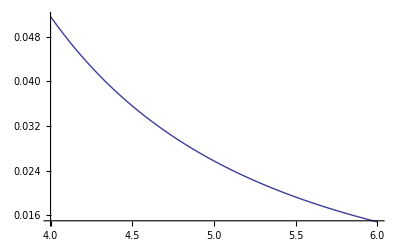

```mathematica
Plot[Abs[Φ[0,y,0.1,4,2]],{y,4,6}]
```

```mathematica
Needs["VectorAnalysis`"]
```

```mathematica
Grad[Φ[x,y,z,W,L],Cartesian[x,y,z]]//Simplify
```

{z ((L-y)/((W^2+2 W x+x^2+z^2) √((W+x)^2+(L-y)^2+z^2))+(-L+y)/((W^2-2 W x+x^2+z^2) √(L^2+W^2-2 W x+x^2-2 L y+y^2+z^2))-(L+y)/((W^2-2 W x+x^2+z^2) √((W-x)^2+(L+y)^2+z^2))+(L+y)/((W^2+2 W x+x^2+z^2) √((W+x)^2+(L+y)^2+z^2))),z (-(W+x)/(√((W+x)^2+(L-y)^2+z^2) (L^2-2 L y+y^2+z^2))+(-W+x)/((L^2-2 L y+y^2+z^2) √(L^2+W^2-2 W x+x^2-2 L y+y^2+z^2))+(W-x)/((L^2+2 L y+y^2+z^2) √((W-x)^2+(L+y)^2+z^2))+(W+x)/((L^2+2 L y+y^2+z^2) √((W+x)^2+(L+y)^2+z^2))),-((W-x) (L-y) (L^2+W^2-2 W x+x^2-2 L y+y^2+2 z^2))/((W^2-2 W x+x^2+z^2) (L^2-2 L y+y^2+z^2) √(L^2+W^2-2 W x+x^2-2 L y+y^2+z^2))-((W+x) (L-y) (L^2+W^2+2 W x+x^2-2 L y+y^2+2 z^2))/((W^2+2 W x+x^2+z^2) √((W+x)^2+(L-y)^2+z^2) (L^2-2 L y+y^2+z^2))-((W-x) (L+y) (L^2+W^2-2 W x+x^2+2 L y+y^2+2 z^2))/((W^2-2 W x+x^2+z^2) (L^2+2 L y+y^2+z^2) √((W-x)^2+(L+y)^2+z^2))-((W+x) (L+y) (L^2+W^2+2 W x+x^2+2 L y+y^2+2 z^2))/((W^2+2 W x+x^2+z^2) (L^2+2 L y+y^2+z^2) √((W+x)^2+(L+y)^2+z^2))}

```mathematica
Ex[x_,y_,z_,W_,L_]:=z ((L-y)/(((W+x)^2+z^2) √((W+x)^2+(L-y)^2+z^2))-(L-y)/(((W-x)^2+z^2) √((L-y)^2+(W-x)^2+z^2))-(L+y)/(((W-x)^2+z^2) √((W-x)^2+(L+y)^2+z^2))+(L+y)/(((W+x)^2+z^2) √((W+x)^2+(L+y)^2+z^2)))
Ey[x_,y_,z_,W_,L_]:=z ((W-x)/(((L+y)^2+z^2) √((W-x)^2+(L+y)^2+z^2))-(W-x)/(((L-y)^2+z^2) √((L-y)^2+(W-x)^2+z^2))-(W+x)/(((L-y)^2+z^2)√((W+x)^2+(L-y)^2+z^2))+(W+x)/(((L+y)^2+z^2) √((W+x)^2+(L+y)^2+z^2)))
Ez[x_,y_,z_,W_,L_]:=-((W-x) (L-y) ((L-y)^2+(W-x)^2+2 z^2))/(((W-x)^2+z^2) ((L-y)^2+z^2) √((W-x)^2+(L-y)^2+z^2))-((W+x) (L-y) ((L-y)^2+(W+x)^2+2 z^2))/(((W+x)^2+z^2) ((L-y)^2+z^2)√((W+x)^2+(L-y)^2+z^2))-((W-x) (L+y) ((L+y)^2+(W-x)^2+2 z^2))/(((W-x)^2+z^2) ((L+y)^2+z^2) √((W-x)^2+(L+y)^2+z^2))-((W+x) (L+y) ((L+y)^2+(W+x)^2+2 z^2))/(((W+x)^2+z^2) ((L+y)^2+z^2) √((W+x)^2+(L+y)^2+z^2))
```

```mathematica
Manipulate[
StreamDensityPlot[{-Ey[0,y,z,W,L],-Ez[0,y,z,W,L]},{y,-5,5},{z,0.1,4},
StreamPoints->Fine, StreamColorFunction->"Rainbow",ColorFunction->Hue,
AspectRatio->0.4,ImageSize->700]
,
{{W,1},0,5},
{{L,3},0,5}]
```